```mathematica
(*Mathematica*)
```

```mathematica
(*Testing a Bell Inequality with a Remote Quantum Processor
Jed Brody,Emory University,Atlanta,GA
Robert Avram,Saint Ann’s School,Brooklyn,NY:https://scholar.google.com/citations?view_op=view_citation&hl=en&user=6BHlRbMAAAAJ&citation_for_view=6BHlRbMAAAAJ:KlAtU1dfN6UC*)
```

```mathematica
(* using the averages as an hidden vacuum point in a fuzzy logic quantum: and numbers instead of bits*)
```

```mathematica
(*adding interpolated true vacuum values:-1/9*)
```

```mathematica
(*adding negative -01,and 100 (-1,-0.5,3.5,4) and between*)
```

```mathematica
v0={-1.0,-0.5,0,0.5,1,1.5,2,2.5,3,3.5,4.0}

u0={9525.682539682628,3013.015873015902,413,-(113+7/9),100,256,90,-(113+7/9),421,3013.015873015902,9525.682539682628}
```

{-1.,-0.5,0,0.5,1,1.5,2,2.5,3,3.5,4.}

{9525.68,3013.02,413,-1024/9,100,256,90,-1024/9,421,3013.02,9525.68}

```mathematica
u0*
```

```mathematica
Apply[Plus,v0]/11.
```

1.5

```mathematica
Apply[Plus,u0]/11.
```

2375.44

```mathematica
2375.440115440137/1024
```

```mathematica
Table[BaseForm[v0[[i]],2],{i,Length[v0]}]
```

{-1._2,-0.1_2,0_2,0.1_2,1_2,1.1_2,10_2,10.1_2,11_2,11.1_2,100._2}

```mathematica
(*Using 2*Sqrt[2] as the true scale of the probabilities*)
```

```mathematica
w=Table[{v0[[i]],u0[[i]]/(2*Sqrt[2]*1024.)},{i,Length[u0]}]
```

{{-1.,3.2889},{-0.5,1.04029},{0,0.142595},{0.5,-0.0392837},{1,0.0345267},{1.5,0.0883883},{2,0.031074},{2.5,-0.0392837},{3,0.145357},{3.5,1.04029},{4.,3.2889}}

```mathematica
(* making the Mexican hat of the Higgs hidden variable*)
```

```mathematica
f[x_]=Fit[w,Table[x^i,{i,0,4}],x]
```

0.143807-0.896988 x+1.39533 x^2-0.730841 x^3+0.121804 x^4

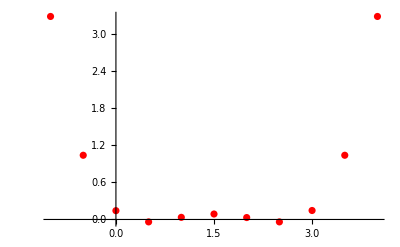

```mathematica
g1=ListPlot[w,PlotStyle->Red, ImageSize->Full]
```

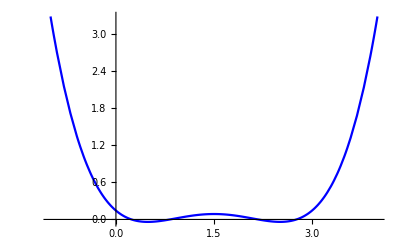

```mathematica
g2=Plot[f[x],{x,-1,4},PlotStyle->Blue, ImageSize->Full,PlotRange->All]
```

```mathematica
(*false vacuum as the average*)
```

```mathematica
f[1.5]
```

0.0878602

```mathematica
%*2*Sqrt[2]
```

0.248506

```mathematica
(*true vacuum states*)
```

```mathematica
f[0.5]
```

-0.0395967

```mathematica
%*2*Sqrt[2]
```

-0.111996

```mathematica
%*9
```

-1.00797

```mathematica
f[2.5]
```

-0.0392876

```mathematica
%*2*Sqrt[2]
```

-0.111122

```mathematica
%*9
```

-1.0001

```mathematica
f[-0.5]
```

1.0401

```mathematica
%*2*Sqrt[2]
```

2.94185

```mathematica
%*1024
```

3012.46

```mathematica
f[3.5]
```

1.04049

```mathematica
%*2*Sqrt[2]
```

2.94294

```mathematica
%*1024
```

3013.58

```mathematica
(*external bits:-01 and 100*)
```

```mathematica
f[-1.]
```

3.28877

```mathematica
%*2*Sqrt[2]
```

9.30205

```mathematica
%*1024
```

9525.3

```mathematica
f[4.0]
```

3.28904

```mathematica
%*2*Sqrt[2]
```

9.3028

```mathematica
%*1024
```

9526.07

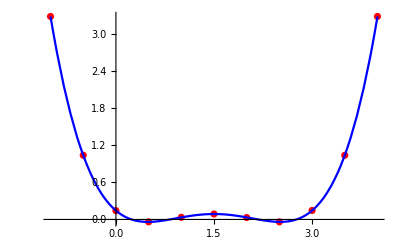

```mathematica
Show[{g1,g2},PlotRange->All]
```

```mathematica
(*end*)
```